```mathematica
vmean=402;
b=6.9;
c=170;
fa[a_]=vmean/(1+((2*(vmean*Tan[a]-b))/c)^2)*(1+Tan[a]^2);
```

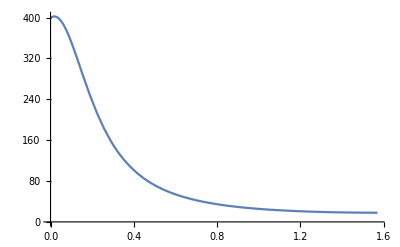

```mathematica
Plot[fa[a],{a,0,Pi/2}]
```

```mathematica
k=1.38064852*10^(-23);
T=100+273.15;
mass=1.443*10^-25;
u=Sqrt[2*k*T/mass]
```

267.218

```mathematica
(* can ignore the  codes below*)
```

```mathematica
vl[v_,a_]=v/(Abs[Sin[phi-a]]+0.001);
```

```mathematica
flo[v_]:=NIntegrate[fa[a]*vl[v,a]^2*Exp[-vl[v,a]^2/u^2],{a,-Pi/2,Pi/2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in a near {a} = {0.490825}. NIntegrate obtained 155.662 and 8.21795 for the integral and error estimates.

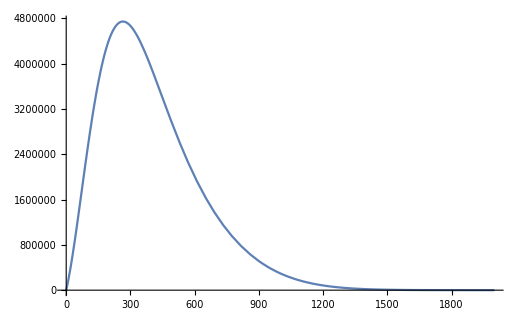

```mathematica
Plot[flo[v*8/17],{v,0,2000}]
```

```mathematica
flo[v_]:=NIntegrate[vl^2*Exp[-vl^2/u^2]*fa[phi-ArcSin[v/vl]]/(-Cos[ArcSin[v/vl]])/vl,{vl,1,Infinity},AccuracyGoal->1,Exclusions->(Cos[ArcSin[v/vl]]==0)]
```

```mathematica
Plot[flo[v*8/17],{v,0,1000}]
```

```mathematica
(* can ignore the above codes*)
```

```mathematica
(* here is the working codes*)
```

```mathematica
phi=ArcTan[21.3/38.5]; (*phi for first condition *)
```

```mathematica
phi=ArcTan[8/17]; (*phi for second condition *)
```

```mathematica
k=1.38064852*10^(-23);
T=200+273.15;
mass=1.443*10^-25;
u=Sqrt[2*k*T/mass]
```

300.9

```mathematica
flo[v_]:=NIntegrate[Abs[UnitStep[v/m]*(v/m)^2*Exp[(-(v/m)^2)/u^2]*fa[phi-ArcSin[m]]/(-Cos[ArcSin[m]])/Abs[m]],{m,-1,1},AccuracyGoal->4,Exclusions->(Cos[ArcSin[m]]==0)]
```

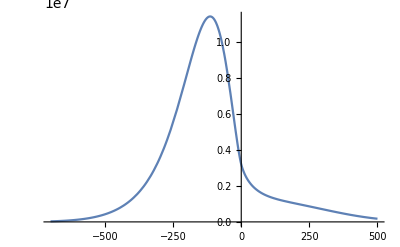

```mathematica
Plot[flo[-v],{v,-700,500}]
```

```mathematica
k=1.38064852*10^(-23);
T=100+273.15;
mass=1.443*10^-25;
u=Sqrt[2*k*T/mass]
```

267.218

```mathematica
ft[t_,l_]=(l/t)^2*Exp[(-(l/t)^2)/u^2]*l/t^2;
```

```mathematica
Manipulate[LogPlot[ft[t/10^6,l],{t,l/950*10^6,l/70*10^6},PlotRange->All],{l,1*10^-2,2*10^-2}]
```

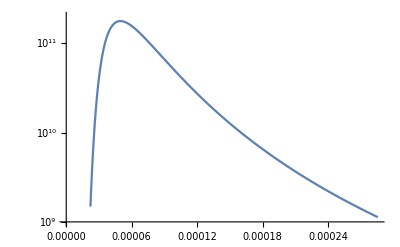

```mathematica
LogPlot[ft[t,0.02],{t,0.02/900,0.02/70},PlotRange->{1*10^9,2*10^11}]
```

```mathematica
D[(l/t)^3*Exp[(-(l/t)^2)/u^2]*l/t^2,t]
```

-(5 ⅇ^(-l^2/(t^2 u^2)) l^4)/t^6+(2 ⅇ^(-l^2/(t^2 u^2)) l^6)/(t^8 u^2)

```mathematica
tmax=l/u/Sqrt[2]

vmax=u*Sqrt[2]
```

```mathematica
2*10^-2/67
```

```mathematica
k=1.38064852*10^(-23);
T=100+273.15;
mass=1.443*10^-25;
u=Sqrt[2*k*T/mass]
```

267.218

```mathematica
Integrate[v^2*Exp[(- v^2)/u^2]*(v*t-L),{v,L/t,(L+d2)/t},Assumptions->{L>0,d2>0,u>0,t>0}]
```

1/(4 t)u^2 (ⅇ^(-(d2+L)^2/(t^2 u^2)) (-2 d2 (d2+L)+2 (-1+ⅇ^((d2 (d2+2 L))/(t^2 u^2))) t^2 u^2)+L √π t u (Erf[L/(t u)]-Erf[(d2+L)/(t u)]))

```mathematica
Integrate[v^2*Exp[(- v^2)/u^2]*d2,{v,(L+d2)/t,Infinity},Assumptions->{L>0,d2>0,u>0,t>0}]
```

1/4 d2 u^2 ((2 ⅇ^(-(d2+L)^2/(t^2 u^2)) (d2+L))/t+√π u Erfc[(d2+L)/(t u)])

```mathematica
d2=1.2*10^-3;
L=2*10^-2;
```

```mathematica
S[t_,u_,d2_]:=1/(4 t)u^2 (ⅇ^(-(d2+L)^2/(t^2 u^2)) (-2 d2 (d2+L)+2 (-1+ⅇ^((d2 (d2+2 L))/(t^2 u^2))) t^2 u^2)+L √π t u (Erf[L/(t u)]-Erf[(d2+L)/(t u)]))+1/4 d2 u^2 ((2 ⅇ^(-(d2+L)^2/(t^2 u^2)) (d2+L))/t+√π u Erfc[(d2+L)/(t u)])
```

```mathematica
u=310
```

310

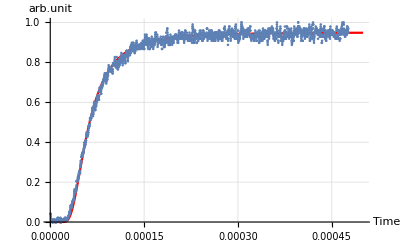

```mathematica
Show[Plot[S[t,u,d2]/S[50000,u,d2]*0.95,{t, 0,500*10^-6},PlotRange->All,GridLines->Automatic,PlotStyle->Red,PlotLegends->"Fitted",AxesLabel->{"Time","arb.unit"}],ListPlot[signal]]
```

```mathematica
T=u^2/2/k*mass-273.15
```

229.05

```mathematica
Clear["Global`*"]
```

```mathematica
signal=Import["C:\\Users\\bocha\\OneDrive - Georgia Institute of Technology\\Publish\\dispenser\\10.20\\ALL0031\\signal.txt","Table"];
```

```mathematica
N[S[480*10^-6,u,d2]/S[50000,u,d2]-S[303*10^-6,u,d2]/S[50000,u,d2]]
```

0.00608189

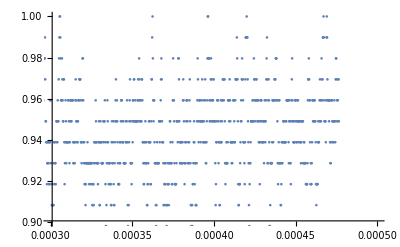

```mathematica
ListPlot[signal,PlotRange->{{300*10^-6,500*10^-6},{0.9,1}}]
```

```mathematica
Integrate[v^2 Exp[-v^2/u^2],{v,44.16,70}]/Integrate[v^2 Exp[-v^2/u^2],{v,0,Infinity}]
```

0.00625264

```mathematica
ArcTan[8/15]*180/Pi
```

(180 ArcTan[8/15])/π

```mathematica
N[(180 ArcTan[8/15])/π]
```

28.0725